```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/benjamin/Documents/Uni/FP2/0407-Optisches Pumpen/data

```mathematica
etalon = Drop[Import["./part2/23-64.1mA-34.0C.tab"], 1];
etalon1 =Transpose[{etalon[[All,1]],etalon[[All,2]]}];
etalon2 =Transpose[{etalon[[All,1]],etalon[[All,3]]}];
```

```mathematica
{fitstart, fitend} = {0.00025, 0.004};
etalon1part = Select[etalon1, #[[1]] ≥ fitstart && #[[1]]≤ fitend&];
nlm = NonlinearModelFit[etalon1part, a + b x, {a, b}, x]
Show[
Plot[Normal[nlm], {x, fitstart - 0.001, fitend + 0.001}, PlotStyle-> {Red, Dashed, Thin}, GridLines->{{fitstart, fitend}, {}}, PlotRange->All,  ImageSize->1000, Frame->True], 
ListPlot[{etalon1, etalon2, etalon1part}, PlotStyle->{PointSize[0.0001]}]]
```

FittedModel[-0.0994679+89.2924 x]

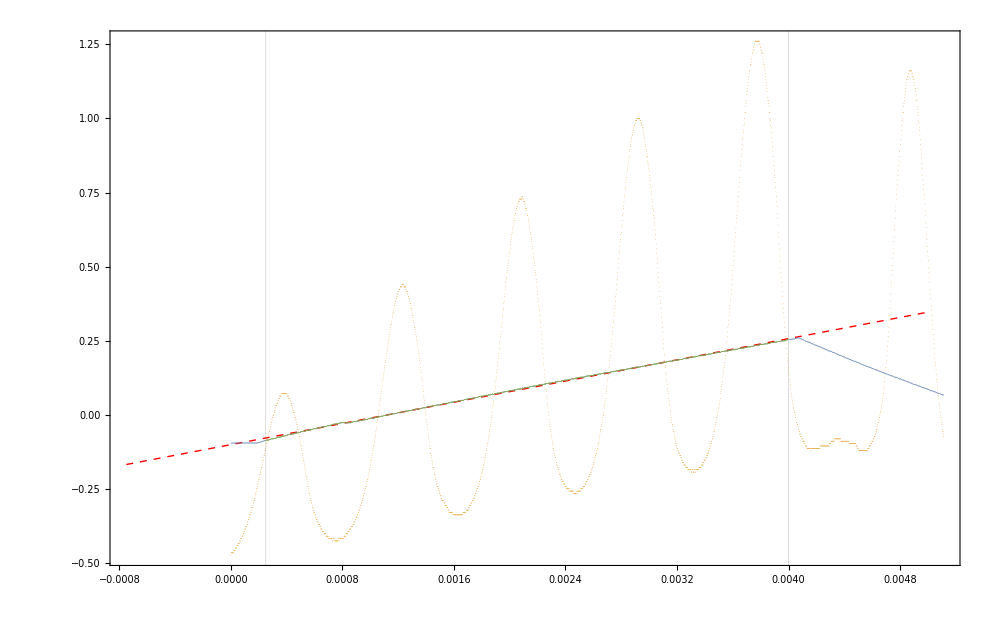
```mathematica
-Graphics-4
```

```mathematica
maxima = Transpose[{{0.0003914,0.0692},{0.001236,0.4405},{0.002086,0.7369},{0.002925,0.999},{0.003787,1.261}}][[1]]
voltage = Normal[nlm] /. x -> maxima
deltanu = Table[n*9924, {n, 0, Length[maxima]-1}];
nuvolt = Transpose[{voltage, deltanu}];
```

{0.0003914,0.001236,0.002086,0.002925,0.003787}

{-0.0645189,0.0108975,0.0867961,0.161712,0.238683}

```mathematica
nlm2 = NonlinearModelFit[nuvolt, a + b x, {a, b}, x]
```

FittedModel[8483.55+131057. x]

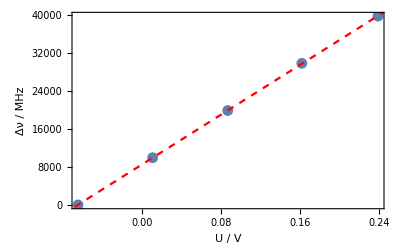

```mathematica
Show[ListPlot[nuvolt, Frame->True, FrameLabel->{"U / V", "Δν / MHz"}], Plot[Normal[nlm2], {x, 1.05*First[voltage], 1.05*Last[voltage]}, PlotStyle->{Red, Dashed}]]
```

```mathematica
freqPerVolts = nlm2["ParameterTableEntries"][[2, 1]]
```

131057.

```mathematica
photo =  Drop[Import["./part2/05-64.1mA-34.0C.tab"], 1];
photo1 =Transpose[{photo[[All,1]],photo[[All,2]]}];
photo2 =Transpose[{photo[[All,1]],photo[[All,3]]}];
```

FittedModel[-0.0292174+24.9083 x]

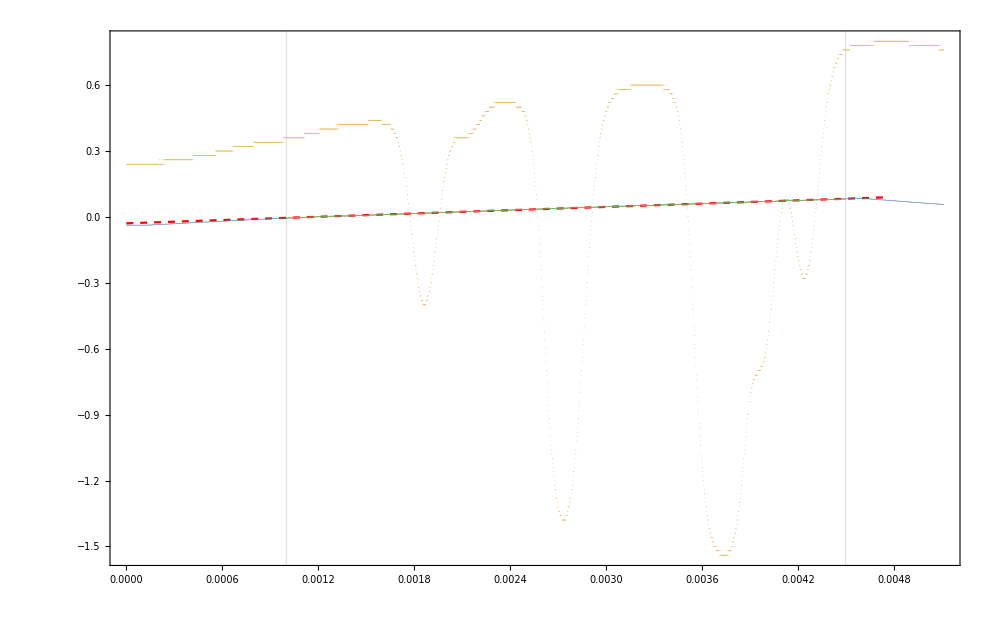

```mathematica
{fitstart2, fitend2} = {0.001, 0.0045};
photo1part =  Select[photo1, #[[1]] ≥ fitstart2 && #[[1]]≤ fitend2&];
nlm3 = NonlinearModelFit[photo1part, a + b x, {a, b}, x]
Show[Plot[Normal[nlm3], {x, 0, 0.00475}, PlotStyle->{Red, Dashed}, PlotRange->All, ImageSize->1000, Frame->True, GridLines->{{fitstart2, fitend2}, {}}],ListPlot[{photo1, photo2, photo1part}, PlotStyle->{PointSize[0.0001]}]]
```

```mathematica
maxima2 = Transpose[{{0.001866,-0.4061},{0.002101,0.3537},{0.002735,-1.382}, {0.002735,-1.382},{0.003746,-1.541},{0.003746,-1.541},{0.003965,-0.691},{0.004244,-0.2895}}][[1]]
```

{0.001866,0.002101,0.002735,0.002735,0.003746,0.003746,0.003965,0.004244}

```mathematica
voltmax = Normal[nlm3] /. x -> maxima2
```

{0.0172615,0.023115,0.0389069,0.0389069,0.0640892,0.0640892,0.0695441,0.0764936}

```mathematica
freq = voltmax * freqPerVolts
```

{2262.24,3029.38,5099.01,5099.01,8399.33,8399.33,9114.23,10025.}

```mathematica
lit = {-3070, -2250, -1480, -1120, 1560, 1920, 3760, 4580}
```

{-3070,-2250,-1480,-1120,1560,1920,3760,4580}

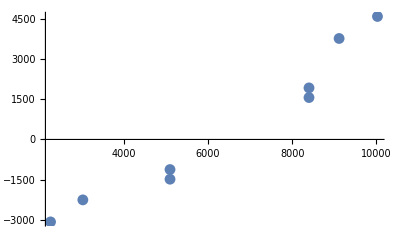

```mathematica
ListPlot[Transpose[{freq, lit}]]
```